## Main Calculation of Energy Bands: Lattice Depth vs. Modulation Frequency

### Calculation of Everything

```mathematica
SetOptions[ListPlot,Frame-> True,Axes->True, LabelStyle-> {FontFamily-> "Helvetica",16}];
SetOptions[ListLogPlot,Frame-> True,Axes->True, LabelStyle-> {FontFamily-> "Helvetica",16}];
SetOptions[Plot,Frame-> True,Axes->True, LabelStyle-> {FontFamily-> "Helvetica",16}];
ClearAll;

(*Main parameter choices*)
latDepthsArr= Range[16]; (*Lattice depths to generate in Er *)
sizeMatrixCalculated= 8; (*Size to use for numerical matrices. See locations variable is used below*)
bFieldUse =203.5;
(*Physical assumptions*)
	(*We assume an isotropic 2D retroreflected lattice as in Fermi2, bouncing at a shallow angle off the microscope substrate, when obtaining the interaction energy. We need to make this assumption to derive a z harmonic state at some lattice depth. 
We assume a potassium 40 mass, and state 1-2 scattering parameters.  *)

(*Inputs that shouldn't change often*)
mAtom=6.642156 10^-26;
aScatbg=167 5.29177 10^-11; (*background scattering length in meters *)
aScat[b_]:=aScatbg*(1-7/(b-202.1)); (*actual scattering length, taking into account correction for some Feshbach effects*)
ℏ=1.05457 10^-34;
θlat = 10.1 Degree;
aSpacing=532.0*10^-9/Cos[θlat]; (*lattice spacing in meters *)
recoilEHz=(ℏ^2/(2mAtom))((2π )/(2aSpacing))^2(1/(2 π ℏ )); 

(*Result arrays *)
	(*Band gaps*)
bandGapMean01Er = {};
bandGapMean02Er = {};
bandGapMin01Er = {};
bandGapMin02Er = {};
	(*Tunneling for single particles*)
tbands000disp10Er={}; (*Usual tunneling*)
tbands000disp20Er={}; (*2 sites away. Note overlapt11Er vanishes by symmtry*)
tbands100disp10Er={}; (*Neighbor tunneling, but with start and end in excited band*)
tbands100disp20Er={}; (*2 sites away tunneling, but with start and end in excited band*)
	(*Interactions between ground band and spatially displaced or excited bands*)
Ubands000disp00Er={}; (*Onsite U overlap with all ground band*)
Ubands000disp10Er={}; (*U overlap with all ground band, neighbor Wannier*)
Ubands000disp11Er={}; (*U overlap with diagonal neighbor Wannier*)
Ubands001disp00Er={}; (*Onsite U overlap with excited Z band*)
Ubands001disp10Er={}; (*U overlap with excited Z band, neighbor Wannier*)
Ubands001disp11Er={}; (*U overlap with excited Z band, with diagonal neighbor Wannier*)
Ubands100disp00Er={}; (*Onsite U overlap with excited X band*)
Ubands100disp10Er={}; (*U overlap with excited X band, neighbor Wannier*)
Ubands100disp11Er={}; (*U overlap with excited X band, with diagonal neighbor Wannier*)
	(*Expected other most important interaction couplings are from being in excited xy states (excited z doesn't lead to enhanced tunneling)*)
	(*Record interaction elements in excited x band*)
UExcitedXbands100disp00Er={}; (*Onsite U overlap with excited X band*)
UExcitedXbands100disp10Er={}; (*U overlap with excited X band, neighbor Wannier*)
UExcitedXbands100disp11Er={}; (*U overlap with excited X band, with diagonal neighbor Wannier*)
	(*Interaction-assisted tunneling where one atom stays in the initial state, but the other tunnels. *)
	(*To first order will only consider nearest neighbor interaction-assisted tunneling (both start on same site, one tunnels)*)
tIntAssistedbands000disp10Er={}; (*Usual tunneling, but with matrix element for second spin given by U times the wavefunction of first spin*)

For[latDepthInd=1,latDepthInd≤ Length[latDepthsArr],latDepthInd++,
V=latDepthsArr[[latDepthInd]]; 

(****************************************)
(****************************************)
(* Set up parameters and units. *)
(****************************************)
(****************************************)
	(*We use units of lattice spacing a = 1 and momentum π/a as the units in real or momentum space*)
	a=1; (*Lattice spacing units of 1 here*)
	(*In fourier space, we use discrete values from q=-1 to q=1 to denote the Brillouin zone, and to convert to real momenta we multiply q by ka to get back units*)
	ka=π/a; (*edge of Brillouin zone, positive and negative*)
	maxMomentumInNumerics=sizeMatrixCalculated; (*This is the maximum wavenumber (in units of pi/a) that we include in the expansion for the unit cell-periodic part of each bloch eigenfunction. In principle it should be infinite to include stuff out to huge real momentum*)
	NLatticeSitesRealSpace=sizeMatrixCalculated; (*NLatticeSitesRealSpace really means the number of sites we are considering in the lattice before periodic boundary conditions*)
	qstep=2/NLatticeSitesRealSpace; (* For a given number of atoms, there are NLatticeSitesRealSpace fourier indices, and q goes from -1 to 1 in qstep steps, so NLatticeSitesRealSpace values of q exist*)

	Nrange=Min[20,NLatticeSitesRealSpace ]; (*This sets size of real space area used to calculate the Wannier function shape (must be large enough to be valid, smaller than system size )*)
	xstep=0.02; (*This is just the ploting resolution for the wavefunction*)
	xlist=Table[(-Nrange/2+i xstep)a, {i,0,Nrange/xstep}]; (*What is this! *)
	xDeltaForNumericalDeriv = xstep/10;
(*Lists to hold the resulting data in*)
energySystem={}; (*This matrix contains, for each q value in BZ, the energy eigenvalue (in Er) and eigenvector *)
(*First band bloch functions and wannier function vs x values, and q values *)
qfunc1={}; 
xfunc1={}; 
(*Second band bloch functions and wannier function*)
qfunc2={}; 
xfunc2={}; 

(****************************************)
(****************************************)
(*Build the Hamiltonian in q space. *)
(****************************************)
(****************************************)
(*It is diagonal for a given Brillouin zone momentum, but we include physical momenta shifted by the lattice momentum up to large momenta*)
For[q=-1,q< 1,q=q+qstep,
diagonalPartOfHamList=Table[(2 qShiftedByMultipleLatticeMomenta +q)^2 + V/2,{qShiftedByMultipleLatticeMomenta,-maxMomentumInNumerics,maxMomentumInNumerics}]; 
	(*This is a list of the diagonal matrix elements in fourier space for a given overall periodicity (wavevector) q. The quadratic part is the kinetic energy, V is potential*)
hamiltonianM=DiagonalMatrix[diagonalPartOfHamList];
(*Now add in the parts coupling the different momenta differing by a lattice momentum*)
For[i=1,i≤ Length[diagonalPartOfHamList]-1,i++,
hamiltonianM[[i,i+1]]=-V/4;
];
For[i=2,i≤ Length[diagonalPartOfHamList],i++,
hamiltonianM[[i,i-1]]=-V/4;
];

(*Get eigenvalues, eigenvectors*)
eigen=Eigensystem[N[hamiltonianM]];
(*Contains eigenvalues and eigenfunctions for the various energy bands. Lowest is the last one. First index is eigenvalues, second is eigenvectors *)

(*Choose the normalization/sign of the eigenvectors to be convenient for creating a localized Bloch wannier functio*)
If[eigen[[2,-1,maxMomentumInNumerics+1]]<0 ,
(*Look at the eigenvector at the end of the eigensystem (which has the lowest energy), and you look at the middle point in the eigenvector, and if it's negative you invert the entire eigenvector*)
eigen[[2,-1]]=-eigen[[2,-1]];
];
If[eigen[[2,-2,maxMomentumInNumerics+1]]<0  ,
(*Do a similar rule for the second Wannier function. Choose to invert it based on whether the background density is positive, but do reverse if q changes sign. *)
eigen[[2,-2]]=-eigen[[2,-2]];
];
If[q<0  ,
eigen[[2,-2]]=-eigen[[2,-2]];
];
AppendTo[energySystem,{q,eigen}];
];
(*At this point, energySystem is a matrix with NLatticeSitesRealSpace entries, one for each value of q. For that q, each entry in energySystem is a matrix of eigenenergies and vectors. Vectors have dimension 2maxMomentumInNumerics+1*)
AppendTo[bandGapMean01Er,{V,(Mean[#[[2,1,-2]]&/@energySystem]-Mean[#[[2,1,-1]]&/@energySystem])}];
AppendTo[bandGapMean02Er,{V,(Mean[#[[2,1,-3]]&/@energySystem]-Mean[#[[2,1,-1]]&/@energySystem])}];
AppendTo[bandGapMin01Er,{V,(Min[#[[2,1,-2]]&/@energySystem]-Max[#[[2,1,-1]]&/@energySystem])}];
AppendTo[bandGapMin02Er,{V,(Min[#[[2,1,-3]]&/@energySystem]-Max[#[[2,1,-1]]&/@energySystem])}];

(****************************************)
(****************************************)
(*Build the Wannier function in real space. *)
(****************************************)
(****************************************)
For[xInd=1,xInd≤ Length[xlist],xInd++,
ϕx1=0; (*This contains the value of the Wannier function at a given value of x, and will be saved later.*)
ϕx2=0;  (*second band*)
For[qIndInEigensystem=1,qIndInEigensystem≤ Length[energySystem],qIndInEigensystem++,
(*Loop through Each bloch state and get bloch wavefunction value at x, and then construct the Wannier function from that*)
ϕq1=0; (*first band*)
ϕq2=0;
q=energySystem[[qIndInEigensystem,1]]; (*extract q from the energySystem matrix*)
qeigen=energySystem[[qIndInEigensystem,2]]; (*extract the entire eigensystem for a given q, this is a matrix with 2 entries, first is a list of eigenenergies, second is a list of eigenvectors. *)
For[qEigenvectorInd=1,qEigenvectorInd≤ Length[qeigen[[2,-1]]],qEigenvectorInd++, (*qeigen[[2,-1]] is the eigenvector associated with the lowest energy eigenstate. qeigen[[2,-2]] is second band*)
ϕq1=ϕq1+qeigen[[2,-1,qEigenvectorInd]]Exp[I 2 ka (qEigenvectorInd-maxMomentumInNumerics-1) xlist[[xInd]]]; 
ϕq2=ϕq2+qeigen[[2,-2,qEigenvectorInd]]Exp[I 2 ka (qEigenvectorInd-maxMomentumInNumerics-1) xlist[[xInd]]];  (*has minus 2 compared to minus 1 in the above line*)
];
ϕq1=(1/(√(NLatticeSitesRealSpace a)))Exp[I  q ka xlist[[xInd]]]ϕq1;(*Do this outside of loop since it seems to slow things down inside loop*)
ϕq2=(1/(√(NLatticeSitesRealSpace a)))Exp[I  q ka xlist[[xInd]]]ϕq2;
AppendTo[qfunc1,{q,xlist[[xInd]],ϕq1}]; 
AppendTo[qfunc2,{q,xlist[[xInd]],ϕq2}]; 

(* Now add this Bloch function to the sum over the bloch functions (with normalization) to get the Wannier Function*)
ϕx1= ϕx1 + (1/(√NLatticeSitesRealSpace))ϕq1; 
ϕx2= ϕx2 + (I/(√NLatticeSitesRealSpace))ϕq2;  
 ];
AppendTo[xfunc1,{xlist[[xInd]],ϕx1}]; (*A list containing the Wannier Function value at that x*)
AppendTo[xfunc2,{xlist[[xInd]],ϕx2}]; (*second band*)
];
(*Define our functions from interpolation*)
wannier1OfX = Interpolation[{#[[1]],Re[#[[2]]]}&/@xfunc1]; (*Index 1 is the x position, index 2 is the value of the wavefunction. *)
wannier2OfX = Interpolation[{#[[1]],Re[#[[2]]]}&/@xfunc2]; (*Second band *)

(****************************************)
(****************************************)
(*Calculate tunneling from <w1|ham|w2>*)
(****************************************)
(****************************************)
(*Now calculate t from the overlap of the wannier functions*)
	(*Take wannier functions displaced by one lattice site and find the NEGATIVE of the overlap between them with the total hamiltonian between them. *)
	(*This total Hamiltonian operator is -ℏ^2/2m grad^2 + V(x), where V(x) is  V sin^2(2π x/a). *)
	(*We do everything in units where the lattice spacing is 1, and in units of Recoil energy, which leaves a factor of (π/a)^2 in the Kinetic term below *)
	(*First find the second derivative of xfunc1. This is primarily a real function so we use the real part*)
(*Define our functions from interpolation*)
wannier1OfX = Interpolation[{#[[1]],Re[#[[2]]]}&/@xfunc1]; (*Index 1 is the x position, index 2 is the value of the wavefunction. *)
wannier2OfX = Interpolation[{#[[1]],Re[#[[2]]]}&/@xfunc2]; (*Second band *)
wannier1OfX2ndDeriv[x_] := 1/xDeltaForNumericalDeriv((wannier1OfX[x+xDeltaForNumericalDeriv] - wannier1OfX[x])/xDeltaForNumericalDeriv- (wannier1OfX[x] - wannier1OfX[x - xDeltaForNumericalDeriv])/xDeltaForNumericalDeriv);
wannier2OfX2ndDeriv[x_] :=  1/xDeltaForNumericalDeriv((wannier2OfX[x+xDeltaForNumericalDeriv] - wannier2OfX[x])/xDeltaForNumericalDeriv- (wannier2OfX[x] - wannier2OfX[x - xDeltaForNumericalDeriv])/xDeltaForNumericalDeriv);
(*Now define a conditional expression which gives a table of the x values and the wannier function table of values, depending on band index, offset, derivative index, etc.  *)
wanFunc[bandIndex_, derivIndex_, offsetDistance_]:= Piecewise[
(*bandIndex is 1 for GS, 2 for first excited band.
derivIndex is 1 for normal function, 2 for numerical second derivative,
offsetDistance is number of sites you want to displace the function by. It gets subtracted from the argument, so you move the physical location by that distance. *)
{
{Table[{x,wannier1OfX[x -offsetDistance]  },{x,xlist}],(bandIndex == 1 && derivIndex == 1)},
{Table[{x,wannier2OfX[x -offsetDistance]  },{x,xlist}],(bandIndex == 2 && derivIndex == 1)},
{Table[{x,wannier1OfX2ndDeriv[x -offsetDistance]  },{x,xlist}],(bandIndex == 1 && derivIndex == 2)},
{Table[{x,wannier2OfX2ndDeriv[x -offsetDistance]  },{x,xlist}],(bandIndex == 2 && derivIndex == 2)}
}
];
(*Define the general function for tunneling! We assume 2 directions for generality *)
wannierOverlapEr[bandIndex1X_,bandIndex1Y_, bandIndex2X_,bandIndex2Y_, offsetDistanceX_, offsetDistanceY_] := 
	(*Offset is of the destination wavefunction, which is bandIndex2. *)
-xstep*Total[(#[[2]]&/@wanFunc[bandIndex2X,1,offsetDistanceX] )*((-(π/a)^-2#[[2]]&/@wanFunc[bandIndex1X,2,0]  ) + V*(Sin[π(#[[1]] &/@ wanFunc[bandIndex1X,1,0])])^2* (#[[2]] &/@ wanFunc[bandIndex1X,1,0]))]*xstep*Total[(#[[2]]&/@wanFunc[bandIndex2Y,1,offsetDistanceY] )* (#[[2]] &/@ wanFunc[bandIndex1Y,1,0])]+-xstep*Total[(#[[2]]&/@wanFunc[bandIndex2Y,1,offsetDistanceY] )*((-(π/a)^-2#[[2]]&/@wanFunc[bandIndex1Y,2,0] ) + V*(Sin[π(#[[1]] &/@ wanFunc[bandIndex1Y,1,0])])^2* (#[[2]] &/@ wanFunc[bandIndex1Y,1,0]))]*xstep*Total[(#[[2]]&/@wanFunc[bandIndex2X,1,offsetDistanceX] )* (#[[2]] &/@ wanFunc[bandIndex1X,1,0])];
 (*Save earest neighbor tunneling in the lowest band since that is generally what we care about most.*)
AppendTo[tbands000disp10Er,{V,wannierOverlapEr[1,1,1,1,1,0] }]; (*Nearest neighbor tunneling in the lowest band.*)
AppendTo[tbands000disp20Er,{V,wannierOverlapEr[1,1,1,1,2,0] }]; (*Next Nearest neighbor tunneling in the lowest band.*)
AppendTo[tbands100disp10Er,{V,wannierOverlapEr[2,1,2,1,1,0] }]; (*Nearest neighbor tunneling starting and ending in the excited band. Band changing tunneling isn't allowed*)
AppendTo[tbands100disp20Er,{V,wannierOverlapEr[2,1,2,1,2,0] }]; (*Next Nearest neighbor tunneling starting and ending in the excited band.*)

(****************************************)
(****************************************)
(*Final calculation of U in real units, assuming realistic lattice geometry*)
(****************************************)
(****************************************)
(*For this we also need the z wavefunction, if we want to calculate U coupling to excited z states as well*)
(*For the z wavefunction we assume a harmonic oscillator state, which is a realtively good approximation because we are very deep in z in units of the z recoil energy, and therefore in the harmonic regime.*)
lzHarmOscLength = 1/π 1/(√(√2 Tan[θlat]))1/V^(1/4); (*Comes from assuming the potential is from both the x and y lattices in the z direction, with a bouncing angle θlat. This harmonic oscillator length is in units of the lattice spacing horiz aSpacing*)
zWaveFunc[bandIndex_]:= Piecewise[
(*bandIndex is 1 for GS, 2 for first excited band.
derivIndex is 1 for normal function, 2 for numerical second derivative,
offsetDistance is number of sites you want to displace the function by. It gets subtracted from the argument, so you move the physical location by that distance. *)
{
{Table[{x,(π lzHarmOscLength^2)^(-1/4)ⅇ^(-(1/2)(x/lzHarmOscLength)^2) },{x,xlist}],(bandIndex == 1 )},
{Table[{x,(π lzHarmOscLength^2)^(-1/4)√2 x/lzHarmOscLength ⅇ^(-(1/2)(x/lzHarmOscLength)^2)  },{x,xlist}],(bandIndex == 2 )},
{Table[{x,(π lzHarmOscLength^2)^(-1/4)1/(√2)(2(x/lzHarmOscLength)^2-1)ⅇ^(-(1/2)(x/lzHarmOscLength)^2)  },{x,xlist}],(bandIndex == 3 )}
}
];
(*Define the general function for interaction! We assume 2 directions of offset for generality, and 3 band indices  *)
UinUnitsOfEr[bandIndex1X_,bandIndex1Y_,bandIndex1Z_, bandIndex2X_,bandIndex2Y_,bandIndex2Z_, offsetDistanceX_, offsetDistanceY_] := 
(*NOTE WELL: This value for the interaction in recoil energy units must be multiplied by aScat/aSpacing to get actual energy!!! I'm leaving it out so we can evaluate at any interaction strength easily*)8/π(xstep Total[((Abs[#[[2]]])^2&/@wanFunc[bandIndex1X,1,0])((Abs[#[[2]]])^2&/@wanFunc[bandIndex2X,1,offsetDistanceX])])*(xstep Total[((Abs[#[[2]]])^2&/@wanFunc[bandIndex1Y,1,0])((Abs[#[[2]]])^2&/@wanFunc[bandIndex2Y,1,offsetDistanceY])])*(xstep Total[((Abs[#[[2]]])^2&/@zWaveFunc[bandIndex1Z])((Abs[#[[2]]])^2&/@zWaveFunc[bandIndex2Z])]);
(*To derive this, we have an integral of psi^4 times other things, and we add a factor of 1/aSpacing^3 to convert each of the linear numerical integrals over the xstep variable in units of lattice spacing to real meters, but then we divide by recoil energy which leaves us with (8/π)*(ascat/aSpacing) as a final scaling parameter for the numerical integrals. Then we leave out the ascat/aSpacing term to have it be added at the end of the calculation*)
AppendTo[Ubands000disp00Er,{V,UinUnitsOfEr[1,1,1,1,1,1,0,0] }];
AppendTo[Ubands000disp10Er,{V,UinUnitsOfEr[1,1,1,1,1,1,1,0] }];
AppendTo[Ubands000disp11Er,{V,UinUnitsOfEr[1,1,1,1,1,1,1,1]  }];
AppendTo[Ubands001disp00Er,{V,UinUnitsOfEr[1,1,1,1,1,2,0,0] }];
AppendTo[Ubands001disp10Er,{V,UinUnitsOfEr[1,1,1,1,1,2,1,0] }];
AppendTo[Ubands001disp11Er,{V,UinUnitsOfEr[1,1,1,1,1,2,1,1]  }];
AppendTo[Ubands100disp00Er,{V,UinUnitsOfEr[1,1,1,2,1,1,0,0] }];
AppendTo[Ubands100disp10Er,{V,UinUnitsOfEr[1,1,1,2,1,1,1,0] }];
AppendTo[Ubands100disp11Er,{V,UinUnitsOfEr[1,1,1,2,1,1,1,1]  }];
AppendTo[UExcitedXbands100disp00Er,{V,UinUnitsOfEr[2,1,1,2,1,1,0,0]  }];
AppendTo[UExcitedXbands100disp10Er,{V,UinUnitsOfEr[2,1,1,2,1,1,1,0]  }];
AppendTo[UExcitedXbands100disp11Er,{V,UinUnitsOfEr[2,1,1,2,1,1,1,1]  }];

(*Derive interaction-assisted tunneling to nearest neighbor, from initial state with 2 atoms on same site. Same as U operator, but with 2nd particle different initial and final states*)
tIntAssistedinUnitsOfEr = 
(*NOTE WELL: This value for the interaction in recoil energy units must be multiplied by aScat/aSpacing to get actual energy!!! I'm leaving it out so we can evaluate at any interaction strength easily*)8/π(xstep Total[((Abs[#[[2]]])^2&/@wanFunc[1,1,0])((#[[2]])&/@wanFunc[1,1,0])((Conjugate[#[[2]]])&/@wanFunc[1,1,1])])*(xstep Total[((Abs[#[[2]]])^2&/@wanFunc[1,1,0])((Abs[#[[2]]])^2&/@wanFunc[1,1,0])])*(xstep Total[((Abs[#[[2]]])^2&/@zWaveFunc[1])((Abs[#[[2]]])^2&/@zWaveFunc[1])]);
AppendTo[tIntAssistedbands000disp10Er,{V,tIntAssistedinUnitsOfEr }];

If[True,
(****************************************)
(****************************************)
(*Plot Band structure to compare to analytic theory*)
(****************************************)
(****************************************)
(*Plot with lowest energy of lowest band subtracted off *)
energyInErVsLowestUnfoldedBZ[fractionFromCenterToEdgeOfBand_,trapDepthErxy_]:= (MathieuCharacteristicA[Abs[fractionFromCenterToEdgeOfBand],trapDepthErxy/4]-MathieuCharacteristicA[0,trapDepthErxy/4]) ;(*ie 0 fractionFromCenterToEdgeOfBand is center, 1 fractionFromCenterToEdgeOfBand is edge of Brillouin Zone*)
pltTheory = Plot[{
energyInErVsLowestUnfoldedBZ[Abs[x],V],
energyInErVsLowestUnfoldedBZ[2-Abs[x],V],
energyInErVsLowestUnfoldedBZ[2+Abs[x],V]
},{x,-1,1}, ImageSize -> Large, GridLines -> All, PlotStyle -> {Automatic, Automatic, Automatic, Dashed, Dashed}, AxesLabel -> {"Momentum [Brillouin Zone]", "Energy [Er]"}, PlotLabels -> {"0th band", "1st band", "2nd band"}];
(*Now plot the lowest energy eigenvalue (-1 index in eigenenergy wave) vs. the q value which goes from -1 to 1, but really is the k vector*)
minEplot = Min[#[[2,1,-1]]&/@energySystem];
pltSim  = ListPlot[{{#[[1]],#[[2,1,-1]]-minEplot }&/@energySystem,{#[[1]],#[[2,1,-2]]-minEplot }&/@energySystem,{#[[1]],#[[2,1,-3]]-minEplot }&/@energySystem},PlotRange-> {Full,{0,20}},FrameLabel->{"q = k/(π/a)","E / Er"}, Joined -> False]; (*ListPlot {x,y} is the format*)
Print[Show[pltTheory,pltSim, ImageSize -> Medium]];
];

Print["Finished calculation for lattice depth of: ",latDepthsArr[[latDepthInd]], " at ", TimeObject[]];
];

(*Set up nice interpolating functions*)
bandGapMean01ErInt = Interpolation[bandGapMean01Er];
bandGapMean02ErInt = Interpolation[bandGapMean02Er];
bandGapMin01ErInt = Interpolation[bandGapMin01Er];
bandGapMin02ErInt = Interpolation[bandGapMin02Er];

tErInt = Interpolation[tbands000disp10Er];
tbands000disp20ErInt = Interpolation[tbands000disp20Er];
tbands100disp10ErInt = Interpolation[tbands100disp10Er];
tbands100disp20ErInt = Interpolation[tbands100disp20Er];

UErInt = Interpolation[Ubands000disp00Er];
Ubands000disp10ErInt = Interpolation[Ubands000disp10Er];
Ubands000disp11ErInt = Interpolation[Ubands000disp11Er];
Ubands001disp00ErInt = Interpolation[Ubands001disp00Er];
Ubands001disp10ErInt = Interpolation[Ubands001disp10Er];
Ubands001disp11ErInt = Interpolation[Ubands001disp11Er];
Ubands100disp00ErInt = Interpolation[Ubands100disp00Er];
Ubands100disp10ErInt = Interpolation[Ubands100disp10Er];
Ubands100disp11ErInt = Interpolation[Ubands100disp11Er];
UExcitedXbands100disp00ErInt = Interpolation[UExcitedXbands100disp00Er];
UExcitedXbands100disp10ErInt = Interpolation[UExcitedXbands100disp10Er];
UExcitedXbands100disp11ErInt = Interpolation[UExcitedXbands100disp11Er];

tIntAssistedbands000disp10ErInt = Interpolation[tIntAssistedbands000disp10Er];

(*Put things in Hz units*)
bandGapMean01HzInt[vv_] :=recoilEHz* bandGapMean01ErInt[vv];
bandGapMean02HzInt[vv_] :=recoilEHz* bandGapMean02ErInt[vv];
bandGapMin01HzInt[vv_] :=recoilEHz* bandGapMin01ErInt[vv];
bandGapMin02HzInt[vv_] :=recoilEHz* bandGapMin02ErInt[vv];
tHzInt[vv_] :=recoilEHz* tErInt[vv];
tbands000disp20HzInt[vv_] :=recoilEHz*tbands000disp20ErInt[vv];
tbands100disp10HzInt[vv_] :=recoilEHz*tbands100disp10ErInt[vv];
tbands100disp20HzInt[vv_] :=recoilEHz*tbands100disp20ErInt[vv];
UHzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing UErInt[vv];
Ubands000disp10HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands000disp10ErInt[vv];
Ubands000disp11HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands000disp11ErInt[vv];
Ubands001disp00HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands001disp00ErInt[vv];
Ubands001disp10HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands001disp10ErInt[vv];
Ubands001disp11HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands001disp11ErInt[vv];
Ubands100disp00HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands100disp00ErInt[vv];
Ubands100disp10HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands100disp10ErInt[vv];
Ubands100disp11HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing Ubands100disp11ErInt[vv];
UExcitedXbands100disp00HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing UExcitedXbands100disp00ErInt[vv];
UExcitedXbands100disp10HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing UExcitedXbands100disp10ErInt[vv];
UExcitedXbands100disp11HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing UExcitedXbands100disp11ErInt[vv];


tIntAssistedbands000disp10HzInt[vv_] :=recoilEHz*aScat[bFieldUse]/aSpacing*tIntAssistedbands000disp10ErInt[vv];

(*Lastly make nice Interaction energy function that allows directly putting in the B field and lattice depth for reference*)
UHzIntVsBAndLatticeDepth[vv_, bb_] :=recoilEHz*aScat[bb]/aSpacing UErInt[vv];
tIntAssistedHzIntVsBAndLatticeDepth[vv_, bb_] :=recoilEHz*aScat[bb]/aSpacing*tIntAssistedbands000disp10ErInt[vv];
```

InterpolatingFunction::dmval: Input value {-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.98} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-4.96} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

Finished calculation for lattice depth of: 1 at 10:02:46TimeObject[{10,2,46.002257},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 2 at 10:02:46TimeObject[{10,2,46.97453},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 3 at 10:02:48TimeObject[{10,2,48.042405},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 4 at 10:02:49TimeObject[{10,2,49.070148},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 5 at 10:02:50TimeObject[{10,2,50.105727},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 6 at 10:02:51TimeObject[{10,2,51.197948},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 7 at 10:02:52TimeObject[{10,2,52.242631},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 8 at 10:02:53TimeObject[{10,2,53.329894},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 9 at 10:02:54TimeObject[{10,2,54.444659},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 10 at 10:02:55TimeObject[{10,2,55.708646},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 11 at 10:02:56TimeObject[{10,2,56.889148},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 12 at 10:02:58TimeObject[{10,2,58.171353},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 13 at 10:02:59TimeObject[{10,2,59.574769},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 14 at 10:03:00TimeObject[{10,3,0.834572},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 15 at 10:03:02TimeObject[{10,3,2.101945},Instant,None]

-Graphics-

Finished calculation for lattice depth of: 16 at 10:03:03TimeObject[{10,3,3.332557},Instant,None]

### Plots to analyze results

#### Basic Data in Recoil Energies

First generate a large table with everything in units of Recoil energies that should be correct regardless of physical system

```mathematica
maxErForTab= Max[latDepthsArr];
```

```mathematica
Print["Usual Hubbard model parameters"]
tab = Table[{ErValTest,
tErInt[ErValTest],
UErInt[ErValTest],
bandGapMean01ErInt[ErValTest],
bandGapMin01ErInt[ErValTest]
},{ErValTest,1,maxErForTab,0.5}];
Prepend[tab, {"Er","t [Er]", "U [Er(a_s/λ_lat)]","E_(mean gap, 01) [Er]","E_(min gap, 01) [Er]"}]//MatrixForm

Print["Extended tunneling parameters"]
Print["    t_(g, 2) means tunneling in ground band by 2 sites, t_(e, 1) means tunneling in first excited band by 1 site"]
tab = Table[{ErValTest,
tErInt[ErValTest],
tbands000disp20ErInt[ErValTest],
tbands100disp10ErInt[ErValTest],
tbands100disp20ErInt[ErValTest],
tIntAssistedbands000disp10ErInt[ErValTest],
tbands000disp20ErInt[ErValTest]/tErInt[ErValTest],
tbands100disp10ErInt[ErValTest]/tErInt[ErValTest],
tbands100disp20ErInt[ErValTest]/tErInt[ErValTest],
tIntAssistedbands000disp10ErInt[ErValTest]/tErInt[ErValTest]
},{ErValTest,1,maxErForTab,0.5}];
Prepend[tab, {"Er","t=t_(g, 1) [Er]", "t_(g, 2) [Er]","t_(e, 1) [Er]", "t_(e, 2) [Er]","t_(int assist) [Er(a_s/λ_lat)]","t_(g, 2)/t","t_(e, 1)/t","t_(e, 2)/t","t_(int assist)/t [(a_s/λ_lat)]"}]//MatrixForm

Print["Interaction U matrix elements"]
Print["    NOTE WELL: All U values are in units of [Er(a_s/λ_lat)], meaning you have to take this number, multiply by Er and by the scattering length/horizontal lattice spacing to get unit in Hz"]
Print["    U_(gg, 10) stands for interaction matrix element in ground band, displacement 10 in xy. U_(gz, 11) means matrix from ground to higher z state with displacement 11, U_gx means matrix ground to higher x state"]
tab = Table[{ErValTest,
UErInt[ErValTest],
Ubands001disp00ErInt[ErValTest],
Ubands100disp00ErInt[ErValTest],
UExcitedXbands100disp00ErInt[ErValTest],
Ubands000disp10ErInt[ErValTest],
Ubands001disp10ErInt[ErValTest],
Ubands100disp10ErInt[ErValTest],
UExcitedXbands100disp10ErInt[ErValTest],
Ubands000disp11ErInt[ErValTest],
Ubands001disp11ErInt[ErValTest],
Ubands100disp11ErInt[ErValTest],
UExcitedXbands100disp11ErInt[ErValTest]
},{ErValTest,1,maxErForTab,0.5}];
Prepend[tab, {"Er", "U_(gg, 00)","U_(gz, 00)","U_(gx, 00)","U_(xx, 00)","U_(gg, 10)","U_(gz, 10)","U_(gx, 10)","U_(xx, 10)","U_(gg, 11)","U_(gz, 11)","U_(gx, 11)","U_(xx, 11)"}]//MatrixForm

Print["Most important parameters relative to t_g"]
Print["    NOTE WELL: U values and t_(int assist) again in units of [Er(a_s/λ_lat)]"]
tab = Table[{ErValTest,
UErInt[ErValTest]/tErInt[ErValTest],
Ubands001disp00ErInt[ErValTest]/tErInt[ErValTest],
Ubands100disp00ErInt[ErValTest]/tErInt[ErValTest],
UExcitedXbands100disp00ErInt[ErValTest]/tErInt[ErValTest],
Ubands100disp10ErInt[ErValTest]/tErInt[ErValTest],
UExcitedXbands100disp10ErInt[ErValTest]/tErInt[ErValTest],
tbands000disp20ErInt[ErValTest]/tErInt[ErValTest],
tbands100disp10ErInt[ErValTest]/tErInt[ErValTest],
tbands100disp20ErInt[ErValTest]/tErInt[ErValTest],
tIntAssistedbands000disp10ErInt[ErValTest]/tErInt[ErValTest]
},{ErValTest,1,maxErForTab,0.5}];
Prepend[tab, {"Er", "U_(gg, 00)/t","U_(gz, 00)/t","U_(gx, 00)/t","U_(xx, 00)/t","U_(gx, 10)/t","U_(xx, 10)/t","t_(g, 2)/t","t_(e, 1)/t","t_(e, 2)/t","t_(int assist)/t"}]//MatrixForm
```

Usual Hubbard model parameters

(Er | t [Er] | U [Er(a_s/λ_lat)] | E_(mean gap, 01) [Er] | E_(min gap, 01) [Er]
1. | 0.181737 | 1.53857 | 2.12389 | 0.499512
1.5 | 0.162288 | 2.08167 | 2.22679 | 0.748363
2. | 0.144093 | 2.65058 | 2.34966 | 0.996112
2.5 | 0.127262 | 3.23863 | 2.48905 | 1.24242
3. | 0.111905 | 3.83914 | 2.64153 | 1.48696
3.5 | 0.098217 | 4.44418 | 2.80312 | 1.72937
4. | 0.0860492 | 5.05086 | 2.972 | 1.96936
4.5 | 0.0753736 | 5.65402 | 3.14546 | 2.2066
5. | 0.0660226 | 6.25257 | 3.32228 | 2.44083
5.5 | 0.0578644 | 6.84372 | 3.50059 | 2.67177
6. | 0.0507637 | 7.42737 | 3.67963 | 2.89921
6.5 | 0.044575 | 8.00238 | 3.85816 | 3.12289
7. | 0.0391967 | 8.56904 | 4.0357 | 3.34268
7.5 | 0.0345039 | 9.12713 | 4.21148 | 3.55837
8. | 0.0304217 | 9.67704 | 4.38524 | 3.76988
8.5 | 0.0268519 | 10.219 | 4.55652 | 3.97706
9. | 0.0237396 | 10.7534 | 4.72522 | 4.17989
9.5 | 0.0210108 | 11.2805 | 4.89109 | 4.37828
10. | 0.018625 | 11.8008 | 5.05411 | 4.57226
10.5 | 0.0165273 | 12.3147 | 5.21418 | 4.76181
11. | 0.0146877 | 12.8224 | 5.37134 | 4.94699
11.5 | 0.0130656 | 13.3243 | 5.52556 | 5.12782
12. | 0.0116388 | 13.8208 | 5.67692 | 5.30442
12.5 | 0.0103773 | 14.312 | 5.82546 | 5.47684
13. | 0.00926438 | 14.7983 | 5.97126 | 5.64522
13.5 | 0.00827777 | 15.2799 | 6.11439 | 5.80965
14. | 0.007405 | 15.757 | 6.25493 | 5.97026
14.5 | 0.00662934 | 16.2299 | 6.39298 | 6.12719
15. | 0.0059414 | 16.6986 | 6.52861 | 6.28056
15.5 | 0.00532993 | 17.1635 | 6.66193 | 6.43052
16. | 0.00478372 | 17.6247 | 6.79302 | 6.57719)

Extended tunneling parameters

t_(g, 2) means tunneling in ground band by 2 sites, t_(e, 1) means tunneling in first excited band by 1 site

(Er | t=t_(g, 1) [Er] | t_(g, 2) [Er] | t_(e, 1) [Er] | t_(e, 2) [Er] | t_(int assist) [Er(a_s/λ_lat)] | t_(g, 2)/t | t_(e, 1)/t | t_(e, 2)/t | t_(int assist)/t [(a_s/λ_lat)]
1. | 0.181737 | -0.0369677 | -2.71705 | -24.1505 | -0.00866459 | -0.203413 | -14.9505 | -132.887 | -0.0476766
1.5 | 0.162288 | -0.0285126 | -3.16029 | -29.4063 | -0.028706 | -0.175692 | -19.4734 | -181.199 | -0.176884
2. | 0.144093 | -0.0215579 | -3.66806 | -35.2805 | -0.0453526 | -0.149611 | -25.4562 | -244.846 | -0.314746
2.5 | 0.127262 | -0.0159831 | -4.2464 | -41.8172 | -0.0585424 | -0.125592 | -33.3673 | -328.591 | -0.460014
3. | 0.111905 | -0.0116678 | -4.90134 | -49.0608 | -0.0682134 | -0.104265 | -43.7991 | -438.415 | -0.609565
3.5 | 0.098217 | -0.00856073 | -5.64056 | -57.0705 | -0.0739592 | -0.0871614 | -57.4296 | -581.065 | -0.753018
4. | 0.0860492 | -0.00633372 | -6.46514 | -65.8452 | -0.0767514 | -0.0736058 | -75.1331 | -765.204 | -0.891948
4.5 | 0.0753736 | -0.00467168 | -7.38046 | -75.4256 | -0.0772533 | -0.0619804 | -97.9184 | -1000.69 | -1.02494
5. | 0.0660226 | -0.00348412 | -8.38135 | -85.7454 | -0.0759835 | -0.0527716 | -126.947 | -1298.73 | -1.15087
5.5 | 0.0578644 | -0.00258945 | -9.46737 | -96.782 | -0.0735949 | -0.0447502 | -163.613 | -1672.56 | -1.27185
6. | 0.0507637 | -0.00194578 | -10.6297 | -108.445 | -0.0703482 | -0.0383302 | -209.396 | -2136.26 | -1.3858
6.5 | 0.044575 | -0.00145809 | -11.8621 | -120.659 | -0.066681 | -0.032711 | -266.116 | -2706.87 | -1.49593
7. | 0.0391967 | -0.00110427 | -13.1565 | -133.353 | -0.0627149 | -0.0281725 | -335.652 | -3402.16 | -1.6
7.5 | 0.0345039 | -0.000834479 | -14.504 | -146.443 | -0.0587007 | -0.0241851 | -420.36 | -4244.26 | -1.70128
8. | 0.0304217 | -0.000636904 | -15.9001 | -159.898 | -0.0546884 | -0.0209359 | -522.659 | -5256.07 | -1.79768
8.5 | 0.0268519 | -0.000485255 | -17.3376 | -173.66 | -0.0508068 | -0.0180716 | -645.676 | -6467.32 | -1.89212
9. | 0.0237396 | -0.000373111 | -18.8152 | -187.73 | -0.0470703 | -0.0157168 | -792.566 | -7907.86 | -1.98277
9.5 | 0.0210108 | -0.000286476 | -20.3291 | -202.086 | -0.043537 | -0.0136347 | -967.557 | -9618.2 | -2.07213
10. | 0.018625 | -0.000221795 | -21.8801 | -216.745 | -0.0402046 | -0.0119084 | -1174.77 | -11637.3 | -2.15864
10.5 | 0.0165273 | -0.000171516 | -23.4672 | -231.71 | -0.0370933 | -0.0103778 | -1419.91 | -14019.9 | -2.24437
11. | 0.0146877 | -0.000133637 | -25.0918 | -246.997 | -0.0341933 | -0.00909855 | -1708.36 | -16816.6 | -2.32802
11.5 | 0.0130656 | -0.00010402 | -26.7544 | -262.621 | -0.0315056 | -0.00796137 | -2047.7 | -20100.2 | -2.41134
12. | 0.0116388 | -0.000081519 | -28.4562 | -278.591 | -0.0290179 | -0.00700405 | -2444.94 | -23936.4 | -2.4932
12.5 | 0.0103773 | -0.0000638302 | -30.1981 | -294.921 | -0.0267224 | -0.00615097 | -2910.03 | -28420. | -2.57509
13. | 0.00926438 | -0.0000502874 | -31.9808 | -311.615 | -0.0246065 | -0.00542803 | -3452.01 | -33635.8 | -2.65603
13.5 | 0.00827777 | -0.0000395872 | -33.8049 | -328.681 | -0.022659 | -0.00478235 | -4083.82 | -39706.5 | -2.73733
14. | 0.007405 | -0.0000313371 | -35.6707 | -346.118 | -0.0208682 | -0.00423188 | -4817.11 | -46741.1 | -2.81812
14.5 | 0.00662934 | -0.0000247883 | -37.5785 | -363.929 | -0.0192221 | -0.00373918 | -5668.5 | -54896.7 | -2.89955
15. | 0.0059414 | -0.0000197067 | -39.5279 | -382.11 | -0.0177105 | -0.00331685 | -6652.97 | -64313.2 | -2.98086
15.5 | 0.00532993 | -0.0000157296 | -41.519 | -400.658 | -0.0163224 | -0.00295119 | -7789.77 | -75171.3 | -3.06241
16. | 0.00478372 | -0.0000124942 | -43.5515 | -419.571 | -0.0150473 | -0.00261182 | -9104.1 | -87708.1 | -3.14551)

Interaction U matrix elements

NOTE WELL: All U values are in units of [Er(a_s/λ_lat)], meaning you have to take this number, multiply by Er and by the scattering length/horizontal lattice spacing to get unit in Hz

U_(gg, 10) stands for interaction matrix element in ground band, displacement 10 in xy. U_(gz, 11) means matrix from ground to higher z state with displacement 11, U_gx means matrix ground to higher x state

(Er | U_(gg, 00) | U_(gz, 00) | U_(gx, 00) | U_(xx, 00) | U_(gg, 10) | U_(gz, 10) | U_(gx, 10) | U_(xx, 10) | U_(gg, 11) | U_(gz, 11) | U_(gx, 11) | U_(xx, 11)
1. | 1.53857 | 0.769284 | 0.462259 | 0.521055 | 0.0795063 | 0.0397531 | 0.314652 | 1.03873 | 0.00410853 | 0.00205426 | 0.0162598 | 0.0536767
1.5 | 2.08167 | 1.04084 | 0.572847 | 0.65572 | 0.0688678 | 0.0344339 | 0.343412 | 1.55786 | 0.0023611 | 0.00118055 | 0.0114316 | 0.0515165
2. | 2.65058 | 1.32529 | 0.6751 | 0.783263 | 0.057851 | 0.0289255 | 0.359577 | 2.2017 | 0.00126264 | 0.000631321 | 0.00784804 | 0.0480539
2.5 | 3.23863 | 1.61931 | 0.772072 | 0.904013 | 0.0471014 | 0.0235507 | 0.365868 | 3.01617 | 0.000650416 | 0.000325208 | 0.00529119 | 0.0438044
3. | 3.83914 | 1.91957 | 0.866813 | 1.0183 | 0.0372643 | 0.0186321 | 0.365006 | 4.04715 | 0.000361702 | 0.000180851 | 0.0035429 | 0.0392833
3.5 | 4.44418 | 2.22209 | 0.963076 | 1.12605 | 0.0293667 | 0.0146834 | 0.36029 | 5.33664 | 0.000181076 | 0.0000905381 | 0.00235587 | 0.0352398
4. | 5.05086 | 2.52543 | 1.06182 | 1.22879 | 0.0229092 | 0.0114546 | 0.352704 | 6.94235 | 0.000103909 | 0.0000519547 | 0.00159976 | 0.0314884
4.5 | 5.65402 | 2.82701 | 1.16526 | 1.32753 | 0.0178225 | 0.00891124 | 0.344154 | 8.92091 | 0.0000524955 | 0.0000262477 | 0.00107341 | 0.0281185
5. | 6.25257 | 3.12628 | 1.27335 | 1.4237 | 0.0138426 | 0.00692128 | 0.33517 | 11.3176 | 0.0000306461 | 0.000015323 | 0.000742033 | 0.025056
5.5 | 6.84372 | 3.42186 | 1.38697 | 1.51877 | 0.0107313 | 0.00536564 | 0.326828 | 14.1895 | 0.0000158283 | 7.91415×10^-6 | 0.000507803 | 0.022264
6. | 7.42737 | 3.71369 | 1.50557 | 1.61368 | 0.00834221 | 0.00417111 | 0.319396 | 17.5578 | 9.36973×10^-6 | 4.68486×10^-6 | 0.000358736 | 0.0197205
6.5 | 8.00238 | 4.00119 | 1.62914 | 1.70971 | 0.00647674 | 0.00323837 | 0.313478 | 21.4624 | 4.96971×10^-6 | 2.48485×10^-6 | 0.000251854 | 0.0173926
7. | 8.56904 | 4.28452 | 1.75701 | 1.80729 | 0.00505328 | 0.00252664 | 0.309146 | 25.9051 | 2.97999×10^-6 | 1.48999×10^-6 | 0.000182307 | 0.0152766
7.5 | 9.12713 | 4.56356 | 1.88871 | 1.90725 | 0.00393937 | 0.00196968 | 0.306696 | 30.9014 | 1.62413×10^-6 | 8.12064×10^-7 | 0.000131639 | 0.0133594
8. | 9.67704 | 4.83852 | 2.02363 | 2.00964 | 0.00308909 | 0.00154455 | 0.306059 | 36.4499 | 9.86096×10^-7 | 4.93048×10^-7 | 0.0000976998 | 0.0116355
8.5 | 10.219 | 5.10949 | 2.16118 | 2.11485 | 0.00242114 | 0.00121057 | 0.307315 | 42.5518 | 5.51568×10^-7 | 2.75784×10^-7 | 0.0000725233 | 0.0100992
9. | 10.7534 | 5.37668 | 2.30087 | 2.2227 | 0.00190929 | 0.000954647 | 0.310319 | 49.2149 | 3.39002×10^-7 | 1.69501×10^-7 | 0.0000550981 | 0.00873828
9.5 | 11.2805 | 5.64026 | 2.44214 | 2.33327 | 0.00150531 | 0.000752657 | 0.315009 | 56.441 | 1.94229×10^-7 | 9.71147×10^-8 | 0.0000419248 | 0.00754394
10. | 11.8008 | 5.90041 | 2.58462 | 2.44627 | 0.001194 | 0.000596999 | 0.321221 | 64.2495 | 1.20808×10^-7 | 6.0404×10^-8 | 0.0000325009 | 0.00650072
10.5 | 12.3147 | 6.15734 | 2.72784 | 2.56155 | 0.00094705 | 0.000473525 | 0.328821 | 72.6515 | 7.075×10^-8 | 3.5375×10^-8 | 0.0000252454 | 0.00559514
11. | 12.8224 | 6.4112 | 2.87151 | 2.67881 | 0.000755521 | 0.00037776 | 0.337653 | 81.6743 | 4.45167×10^-8 | 2.22584×10^-8 | 0.0000198952 | 0.00481241
11.5 | 13.3243 | 6.66217 | 3.01528 | 2.79777 | 0.000602811 | 0.000301406 | 0.347561 | 91.3387 | 2.65942×10^-8 | 1.32971×10^-8 | 0.0000157084 | 0.00413729
12. | 13.8208 | 6.91038 | 3.15894 | 2.91816 | 0.000483583 | 0.000241791 | 0.35841 | 101.675 | 1.69204×10^-8 | 8.46018×10^-9 | 0.0000125406 | 0.00355757
12.5 | 14.312 | 7.156 | 3.30221 | 3.03965 | 0.000388038 | 0.000194019 | 0.370052 | 112.711 | 1.0292×10^-8 | 5.14599×10^-9 | 0.0000100276 | 0.00305905
13. | 14.7983 | 7.39914 | 3.44495 | 3.16201 | 0.000312948 | 0.000156474 | 0.382378 | 124.476 | 6.61812×10^-9 | 3.30906×10^-9 | 8.08639×10^-6 | 0.00263236
13.5 | 15.2799 | 7.63994 | 3.58695 | 3.28493 | 0.000252479 | 0.000126239 | 0.395258 | 137. | 4.09193×10^-9 | 2.04596×10^-9 | 6.52925×10^-6 | 0.00226573
14. | 15.757 | 7.87849 | 3.72814 | 3.40823 | 0.000204652 | 0.000102326 | 0.408608 | 150.312 | 2.65801×10^-9 | 1.32901×10^-9 | 5.30699×10^-6 | 0.00195225
14.5 | 16.2299 | 8.11493 | 3.86838 | 3.53163 | 0.000165954 | 0.0000829769 | 0.422322 | 164.441 | 1.66809×10^-9 | 8.34046×10^-10 | 4.31784×10^-6 | 0.00168274
15. | 16.6986 | 8.34932 | 4.00761 | 3.65501 | 0.000135161 | 0.0000675805 | 0.436338 | 179.414 | 1.09401×10^-9 | 5.47005×10^-10 | 3.53178×10^-6 | 0.0014522
15.5 | 17.1635 | 8.58177 | 4.14577 | 3.77818 | 0.000110476 | 0.0000552381 | 0.450583 | 195.258 | 7.52586×10^-10 | 3.76293×10^-10 | 2.90086×10^-6 | 0.00125457
16. | 17.6247 | 8.81236 | 4.28279 | 3.90096 | 0.0000901029 | 0.0000450514 | 0.464982 | 212. | 4.60633×10^-10 | 2.30316×10^-10 | 2.37713×10^-6 | 0.00108381)

Most important parameters relative to t_g

NOTE WELL: U values and t_(int assist) again in units of [Er(a_s/λ_lat)]

(Er | U_(gg, 00)/t | U_(gz, 00)/t | U_(gx, 00)/t | U_(xx, 00)/t | U_(gx, 10)/t | U_(xx, 10)/t | t_(g, 2)/t | t_(e, 1)/t | t_(e, 2)/t | t_(int assist)/t
1. | 8.46592 | 4.23296 | 2.54356 | 2.86709 | 1.73136 | 5.71556 | -0.203413 | -14.9505 | -132.887 | -0.0476766
1.5 | 12.8271 | 6.41353 | 3.52983 | 4.04048 | 2.11607 | 9.59938 | -0.175692 | -19.4734 | -181.199 | -0.176884
2. | 18.395 | 9.19748 | 4.68518 | 5.43582 | 2.49545 | 15.2798 | -0.149611 | -25.4562 | -244.846 | -0.314746
2.5 | 25.4485 | 12.7242 | 6.06678 | 7.10355 | 2.87492 | 23.7004 | -0.125592 | -33.3673 | -328.591 | -0.460014
3. | 34.3071 | 17.1536 | 7.74597 | 9.09967 | 3.26175 | 36.166 | -0.104265 | -43.7991 | -438.415 | -0.609565
3.5 | 45.2486 | 22.6243 | 9.8056 | 11.4649 | 3.66831 | 54.3352 | -0.0871614 | -57.4296 | -581.065 | -0.753018
4. | 58.6974 | 29.3487 | 12.3397 | 14.2801 | 4.09887 | 80.6788 | -0.0736058 | -75.1331 | -765.204 | -0.891948
4.5 | 75.0133 | 37.5067 | 15.4598 | 17.6126 | 4.56598 | 118.356 | -0.0619804 | -97.9184 | -1000.69 | -1.02494
5. | 94.7035 | 47.3517 | 19.2866 | 21.5639 | 5.07659 | 171.42 | -0.0527716 | -126.947 | -1298.73 | -1.15087
5.5 | 118.272 | 59.1359 | 23.9693 | 26.2471 | 5.64816 | 245.219 | -0.0447502 | -163.613 | -1672.56 | -1.27185
6. | 146.313 | 73.1564 | 29.6584 | 31.788 | 6.29182 | 345.874 | -0.0383302 | -209.396 | -2136.26 | -1.3858
6.5 | 179.526 | 89.7632 | 36.5483 | 38.3558 | 7.0326 | 481.49 | -0.032711 | -266.116 | -2706.87 | -1.49593
7. | 218.616 | 109.308 | 44.8254 | 46.1082 | 7.88703 | 660.898 | -0.0281725 | -335.652 | -3402.16 | -1.6
7.5 | 264.525 | 132.262 | 54.739 | 55.2763 | 8.88873 | 895.591 | -0.0241851 | -420.36 | -4244.26 | -1.70128
8. | 318.097 | 159.049 | 66.5194 | 66.0595 | 10.0606 | 1198.16 | -0.0209359 | -522.659 | -5256.07 | -1.79768
8.5 | 380.569 | 190.284 | 80.4853 | 78.7598 | 11.4448 | 1584.69 | -0.0180716 | -645.676 | -6467.32 | -1.89212
9. | 452.971 | 226.485 | 96.9211 | 93.6285 | 13.0718 | 2073.11 | -0.0157168 | -792.566 | -7907.86 | -1.98277
9.5 | 536.892 | 268.446 | 116.233 | 111.051 | 14.9928 | 2686.29 | -0.0136347 | -967.557 | -9618.2 | -2.07213
10. | 633.601 | 316.8 | 138.771 | 131.343 | 17.2468 | 3449.63 | -0.0119084 | -1174.77 | -11637.3 | -2.15864
10.5 | 745.114 | 372.557 | 165.051 | 154.99 | 19.8957 | 4395.86 | -0.0103778 | -1419.91 | -14019.9 | -2.24437
11. | 873.003 | 436.502 | 195.505 | 182.385 | 22.9889 | 5560.73 | -0.00909855 | -1708.36 | -16816.6 | -2.32802
11.5 | 1019.8 | 509.902 | 230.781 | 214.133 | 26.6013 | 6990.79 | -0.00796137 | -2047.7 | -20100.2 | -2.41134
12. | 1187.47 | 593.735 | 271.414 | 250.726 | 30.7944 | 8735.85 | -0.00700405 | -2444.94 | -23936.4 | -2.4932
12.5 | 1379.17 | 689.584 | 318.216 | 292.915 | 35.6599 | 10861.3 | -0.00615097 | -2910.03 | -28420. | -2.57509
13. | 1597.33 | 798.665 | 371.848 | 341.308 | 41.274 | 13435.9 | -0.00542803 | -3452.01 | -33635.8 | -2.65603
13.5 | 1845.89 | 922.947 | 433.324 | 396.838 | 47.7493 | 16550.3 | -0.00478235 | -4083.82 | -39706.5 | -2.73733
14. | 2127.88 | 1063.94 | 503.463 | 460.26 | 55.18 | 20298.7 | -0.00423188 | -4817.11 | -46741.1 | -2.81812
14.5 | 2448.18 | 1224.09 | 583.523 | 532.728 | 63.7049 | 24805. | -0.00373918 | -5668.5 | -54896.7 | -2.89955
15. | 2810.56 | 1405.28 | 674.523 | 615.177 | 73.4403 | 30197.2 | -0.00331685 | -6652.97 | -64313.2 | -2.98086
15.5 | 3220.21 | 1610.11 | 777.827 | 708.86 | 84.5381 | 36634.2 | -0.00295119 | -7789.77 | -75171.3 | -3.06241
16. | 3684.31 | 1842.16 | 895.284 | 815.465 | 97.2009 | 44316.9 | -0.00261182 | -9104.1 | -87708.1 | -3.14551)

#### Basic Data in Hz

```mathematica
LogPlot[{tHzInt[V],Abs[UHzInt[V]],Abs[tbands000disp20HzInt[V]],Abs[Ubands000disp10HzInt[V]], Abs[tIntAssistedbands000disp10HzInt[V]]}, {V,1,16}, PlotRange -> All, PlotLabels ->{"t", "U","t_2", "U_1", "t_(int assist)"}, AxesLabel ->{"V [Er]", "Energy [Hz]"},ImageSize -> Large, GridLines -> All]
```

-Graphics-

```mathematica
tab = Table[{ErValTest,
tHzInt[ErValTest],
UHzInt[ErValTest],
4*tHzInt[ErValTest]^2/UHzInt[ErValTest],
tbands000disp20HzInt[ErValTest],
Ubands000disp10HzInt[ErValTest],
UHzInt[ErValTest]/tHzInt[ErValTest],
bandGapMean01HzInt[ErValTest],
bandGapMin01HzInt[ErValTest]
},{ErValTest,1,maxErForTab,0.5}];
Prepend[tab, {"Er","t [Hz]", "U [Hz]", "4t^2/U [Hz]","t_(g, 2) [Hz]","U_(gg, 10) [Hz]", "U/t","E_(mean gap, 01) [Hz]","E_(min gap, 01) [Hz]"}]//MatrixForm

tab = Table[{ErValTest,
tHzInt[ErValTest],
tbands000disp20HzInt[ErValTest],
tbands100disp10HzInt[ErValTest],
tbands100disp20HzInt[ErValTest],
Abs[tIntAssistedbands000disp10HzInt[ErValTest]]
},{ErValTest,1,8,0.5}];
Prepend[tab, {"Er","t [Hz]","t_(g, 2) [Hz]","t_(e, 1) [Hz]","t_(e, 2) [Hz]", "t_(int assist) [Hz]"}]//MatrixForm

tab = Table[{ErValTest,
tHzInt[ErValTest],
UHzInt[ErValTest],
Ubands000disp10HzInt[ErValTest],
Ubands100disp10HzInt[ErValTest],
UExcitedXbands100disp10HzInt[ErValTest]
},{ErValTest,1,maxErForTab,0.5}];
Prepend[tab, {"Er","t [Hz]","U [Hz]","U_(gg, 10) [Hz]","U_(gx, 10) [Hz]","U_(xx, 10) [Hz]"}]//MatrixForm
```

(Er | t [Hz] | U [Hz] | 4t^2/U [Hz] | t_(g, 2) [Hz] | U_(gg, 10) [Hz] | U/t | E_(mean gap, 01) [Hz] | E_(min gap, 01) [Hz]
1. | 776.086 | -429.801 | -5605.48 | -157.866 | -22.2102 | -0.553805 | 9069.82 | 2133.11
1.5 | 693.031 | -581.517 | -3303.71 | -121.76 | -19.2383 | -0.839093 | 9509.25 | 3195.8
2. | 615.332 | -740.443 | -2045.45 | -92.0608 | -16.1607 | -1.20332 | 10033.9 | 4253.79
2.5 | 543.459 | -904.714 | -1305.82 | -68.2542 | -13.1578 | -1.66473 | 10629.2 | 5305.63
3. | 477.878 | -1072.47 | -851.745 | -49.8261 | -10.4098 | -2.24423 | 11280.4 | 6349.89
3.5 | 419.425 | -1241.49 | -566.795 | -36.5576 | -8.20363 | -2.95997 | 11970.4 | 7385.07
4. | 367.463 | -1410.96 | -382.8 | -27.0474 | -6.39971 | -3.83974 | 12691.6 | 8409.92
4.5 | 321.874 | -1579.46 | -262.376 | -19.9499 | -4.97873 | -4.90706 | 13432.3 | 9423.01
5. | 281.942 | -1746.66 | -182.042 | -14.8785 | -3.86693 | -6.19511 | 14187.4 | 10423.3
5.5 | 247.103 | -1911.8 | -127.754 | -11.0579 | -2.99779 | -7.73684 | 14948.9 | 11409.5
6. | 216.781 | -2074.84 | -90.5973 | -8.30925 | -2.3304 | -9.57117 | 15713.5 | 12380.7
6.5 | 190.352 | -2235.47 | -64.8346 | -6.22661 | -1.80928 | -11.7439 | 16475.8 | 13335.9
7. | 167.385 | -2393.77 | -46.8178 | -4.71566 | -1.41164 | -14.301 | 17234. | 14274.5
7.5 | 147.345 | -2549.67 | -34.0601 | -3.56355 | -1.10047 | -17.3041 | 17984.6 | 15195.6
8. | 129.912 | -2703.29 | -24.9728 | -2.71983 | -0.862941 | -20.8086 | 18726.7 | 16098.8
8.5 | 114.668 | -2854.68 | -18.4241 | -2.07223 | -0.676347 | -24.8952 | 19458.1 | 16983.6
9. | 101.377 | -3003.96 | -13.6851 | -1.59333 | -0.533363 | -29.6315 | 20178.5 | 17849.7
9.5 | 89.7241 | -3151.22 | -10.2188 | -1.22336 | -0.420511 | -35.1212 | 20886.8 | 18696.9
10. | 79.5361 | -3296.57 | -7.67583 | -0.94715 | -0.333545 | -41.4475 | 21583. | 19525.3
10.5 | 70.5778 | -3440.12 | -5.79192 | -0.732439 | -0.264559 | -48.7422 | 22266.6 | 20334.8
11. | 62.7221 | -3581.95 | -4.39321 | -0.57068 | -0.211055 | -57.1082 | 22937.7 | 21125.5
11.5 | 55.7951 | -3722.16 | -3.34546 | -0.444205 | -0.168396 | -66.7113 | 23596.3 | 21897.8
12. | 49.7023 | -3860.84 | -2.55936 | -0.348117 | -0.135089 | -77.6793 | 24242.7 | 22651.9
12.5 | 44.3149 | -3998.07 | -1.96476 | -0.27258 | -0.108399 | -90.2195 | 24877. | 23388.2
13. | 39.5625 | -4133.91 | -1.51449 | -0.214747 | -0.0874224 | -104.491 | 25499.6 | 24107.3
13.5 | 35.3493 | -4268.45 | -1.17098 | -0.169052 | -0.0705301 | -120.751 | 26110.8 | 24809.4
14. | 31.6222 | -4401.73 | -0.908702 | -0.133821 | -0.0571696 | -139.197 | 26711. | 25495.3
14.5 | 28.3099 | -4533.82 | -0.707084 | -0.105856 | -0.0463594 | -160.15 | 27300.5 | 26165.5
15. | 25.3721 | -4664.78 | -0.552002 | -0.0841554 | -0.0377573 | -183.855 | 27879.7 | 26820.4
15.5 | 22.7609 | -4794.65 | -0.432197 | -0.0671716 | -0.0308616 | -210.653 | 28449. | 27460.8
16. | 20.4283 | -4923.48 | -0.339042 | -0.0533552 | -0.0251703 | -241.012 | 29008.8 | 28087.1)

(Er | t [Hz] | t_(g, 2) [Hz] | t_(e, 1) [Hz] | t_(e, 2) [Hz] | t_(int assist) [Hz]
1. | 776.086 | -157.866 | -11602.9 | -103132. | 2.42046
1.5 | 693.031 | -121.76 | -13495.6 | -125576. | 8.01905
2. | 615.332 | -92.0608 | -15664. | -150661. | 12.6693
2.5 | 543.459 | -68.2542 | -18133.8 | -178576. | 16.3539
3. | 477.878 | -49.8261 | -20930.6 | -209508. | 19.0555
3.5 | 419.425 | -36.5576 | -24087.4 | -243713. | 20.6606
4. | 367.463 | -27.0474 | -27608.6 | -281184. | 21.4406
4.5 | 321.874 | -19.9499 | -31517.4 | -322096. | 21.5808
5. | 281.942 | -14.8785 | -35791.6 | -366166. | 21.2261
5.5 | 247.103 | -11.0579 | -40429.3 | -413296. | 20.5588
6. | 216.781 | -8.30925 | -45392.9 | -463101. | 19.6518
6.5 | 190.352 | -6.22661 | -50655.9 | -515259. | 18.6274
7. | 167.385 | -4.71566 | -56183.2 | -569471. | 17.5195
7.5 | 147.345 | -3.56355 | -61937.9 | -625370. | 16.3981
8. | 129.912 | -2.71983 | -67899.8 | -682828. | 15.2773)

(Er | t [Hz] | U [Hz] | U_(gg, 10) [Hz] | U_(gx, 10) [Hz] | U_(xx, 10) [Hz]
1. | 776.086 | -429.801 | -22.2102 | -87.8982 | -290.169
1.5 | 693.031 | -581.517 | -19.2383 | -95.9324 | -435.19
2. | 615.332 | -740.443 | -16.1607 | -100.448 | -615.048
2.5 | 543.459 | -904.714 | -13.1578 | -102.206 | -842.569
3. | 477.878 | -1072.47 | -10.4098 | -101.965 | -1130.58
3.5 | 419.425 | -1241.49 | -8.20363 | -100.647 | -1490.79
4. | 367.463 | -1410.96 | -6.39971 | -98.5283 | -1939.35
4.5 | 321.874 | -1579.46 | -4.97873 | -96.1398 | -2492.06
5. | 281.942 | -1746.66 | -3.86693 | -93.63 | -3161.58
5.5 | 247.103 | -1911.8 | -2.99779 | -91.2996 | -3963.84
6. | 216.781 | -2074.84 | -2.3304 | -89.2236 | -4904.8
6.5 | 190.352 | -2235.47 | -1.80928 | -87.5703 | -5995.54
7. | 167.385 | -2393.77 | -1.41164 | -86.3602 | -7236.6
7.5 | 147.345 | -2549.67 | -1.10047 | -85.6757 | -8632.33
8. | 129.912 | -2703.29 | -0.862941 | -85.4979 | -10182.3
8.5 | 114.668 | -2854.68 | -0.676347 | -85.8486 | -11886.9
9. | 101.377 | -3003.96 | -0.533363 | -86.6878 | -13748.2
9.5 | 89.7241 | -3151.22 | -0.420511 | -87.9982 | -15766.8
10. | 79.5361 | -3296.57 | -0.333545 | -89.7335 | -17948.2
10.5 | 70.5778 | -3440.12 | -0.264559 | -91.8566 | -20295.3
11. | 62.7221 | -3581.95 | -0.211055 | -94.3238 | -22815.8
11.5 | 55.7951 | -3722.16 | -0.168396 | -97.0915 | -25515.6
12. | 49.7023 | -3860.84 | -0.135089 | -100.122 | -28403.
12.5 | 44.3149 | -3998.07 | -0.108399 | -103.374 | -31485.8
13. | 39.5625 | -4133.91 | -0.0874224 | -106.818 | -34772.4
13.5 | 35.3493 | -4268.45 | -0.0705301 | -110.416 | -38271.
14. | 31.6222 | -4401.73 | -0.0571696 | -114.145 | -41989.7
14.5 | 28.3099 | -4533.82 | -0.0463594 | -117.976 | -45936.7
15. | 25.3721 | -4664.78 | -0.0377573 | -121.891 | -50119.4
15.5 | 22.7609 | -4794.65 | -0.0308616 | -125.871 | -54545.4
16. | 20.4283 | -4923.48 | -0.0251703 | -129.893 | -59222.3)

#### Analyze at various magnetic fields

Data at 5 Er:

-Graphics-

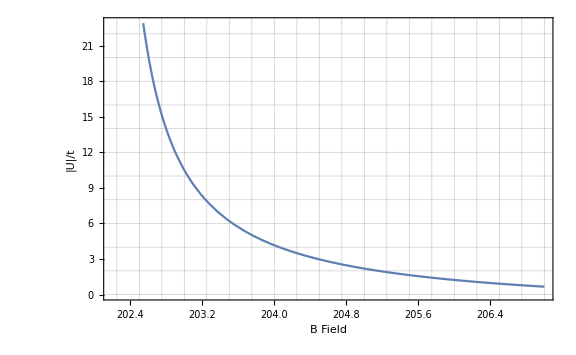

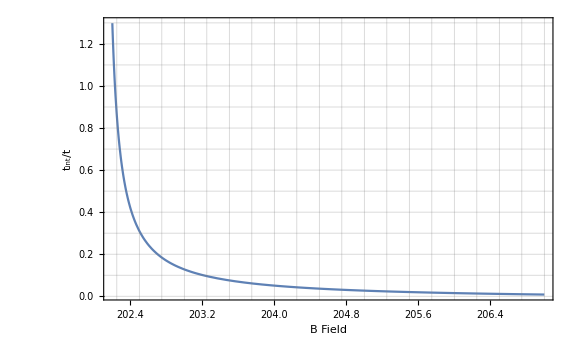

```mathematica
VErTest = 5;
bMinPlot = 202.2;
bMaxPlot = 207;
Print["Data at ", VErTest, " Er:"]
Plot[{Abs[UHzIntVsBAndLatticeDepth[VErTest, b]],tHzInt[VErTest],tIntAssistedHzIntVsBAndLatticeDepth[VErTest,b]}, {b,bMinPlot ,bMaxPlot }, GridLines ->All, FrameLabel -> {"B Field", "Energy [Hz]"}, PlotLabels -> {"|U|", "t", "t_int"}, ImageSize -> Large]
Plot[{Abs[UHzIntVsBAndLatticeDepth[VErTest, b]]/tHzInt[VErTest]}, {b,bMinPlot ,bMaxPlot }, GridLines ->All, FrameLabel -> {"B Field", "|U|/t"}]
Plot[{tIntAssistedHzIntVsBAndLatticeDepth[VErTest,b]/tHzInt[VErTest]}, {b,bMinPlot ,bMaxPlot }, GridLines ->All, FrameLabel -> {"B Field", "t_int/t"}, PlotRange -> All]
```

## Other things for reference

### Analytic energy spectrum for reference

```mathematica
ErTestPlot = 5; 
(*Plot with lowest energy of lowest band subtracted off *)
energyInErVsLowestUnfoldedBZ[fractionFromCenterToEdgeOfBand_,trapDepthErxy_]:= (MathieuCharacteristicA[Abs[fractionFromCenterToEdgeOfBand],trapDepthErxy/4]-MathieuCharacteristicA[0,trapDepthErxy/4]) ;(*ie 0 fractionFromCenterToEdgeOfBand is center, 1 fractionFromCenterToEdgeOfBand is edge of Brillouin Zone*)
pltTheory = Plot[{
energyInErVsLowestUnfoldedBZ[Abs[x],ErTestPlot],
energyInErVsLowestUnfoldedBZ[2-Abs[x],ErTestPlot],
energyInErVsLowestUnfoldedBZ[2+Abs[x],ErTestPlot]
},{x,-1,1}, ImageSize -> Large, GridLines -> All, PlotStyle -> {Automatic, Automatic, Automatic, Dashed, Dashed}, AxesLabel -> {"Momentum [Brillouin Zone]", "Energy [Er]"}, PlotLabels -> {"0th band", "1st band", "2nd band"}]
```

-Graphics-

```mathematica
energyDifferenceInEr[trapDepthErxy_,startBand_,startFromTopOne_,endBand_,endAtTopOne_]:=Module[{startVal=If[startFromTopOne>0.5,startBand+1-0.001,startBand+0.001],endVal=If[endAtTopOne>0.5,endBand+1-0.001,endBand+0.001]},
energyInErVsLowest[endVal,trapDepthErxy]-energyInErVsLowest[startVal,trapDepthErxy]
]
Plot[{recoilEHz*energyDifferenceInEr[Er,0,0,2,0]},{Er,4,6}, PlotLabels->{"Bottom 0th band - Bottom 2nd band"}, ImageSize -> Large, AxesLabel -> {"Lattice depth [Er_xy]", "Energy [Hz]"}]
```

-Graphics-

#### Modulation peak location vs Er

Now make an inverse function to find the supposed maximum excitation frequency vs lattice depth, to invert

```mathematica
ModPeakHzVsEr[ErVal_]:=xHz /. Solve[ErHorizXYInHz*energyDifferenceInEr[ErVal,0,0,2,0] == xHz, xHz][[1]]
latErVsModPeakHzInterpolated = Interpolation[Table[{ModPeakHzVsEr[VEr],VEr},{VEr,0, 20, 0.1}]];
```

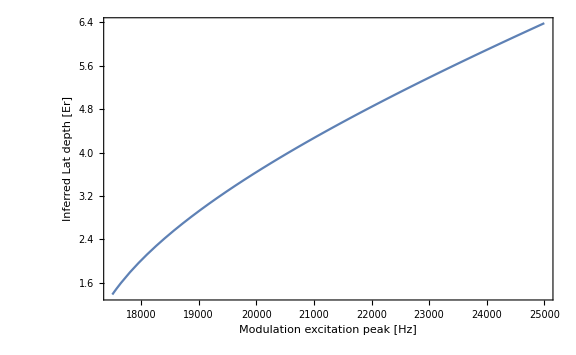

```mathematica
Plot[latErVsModPeakHzInterpolated[modPeakFreqHz],{modPeakFreqHz,17500,25000}, AxesLabel -> {"Modulation excitation peak [Hz]", "Inferred Lat depth [Er]"}, ImageSize -> Large]
```

### Experimental Measurements vs Setpoint Voltage

Measured values

```mathematica
xLatErVsSetpointV={{0.981,latErVsModPeakHzInterpolated[21000]},{1.197,latErVsModPeakHzInterpolated[22500]}}
yLatErVsSetpointV={{0.972,latErVsModPeakHzInterpolated[21000]},{1.222,latErVsModPeakHzInterpolated[23000]}}
xLatSetpointVVsEr=Table[{xLatErVsSetpointV[[ii]][[2]],xLatErVsSetpointV[[ii]][[1]]}, {ii,Table[jj,{jj,Length[xLatErVsSetpointV]}]}]
yLatSetpointVVsEr=Table[{yLatErVsSetpointV[[ii]][[2]],yLatErVsSetpointV[[ii]][[1]]}, {ii,Table[jj,{jj,Length[yLatErVsSetpointV]}]}]
```

{{0.981,4.26848},{1.197,5.11682}}

{{0.972,4.26848},{1.222,5.38219}}

{{4.26848,0.981},{5.11682,1.197}}

{{4.26848,0.972},{5.38219,1.222}}

Linear interpolation

```mathematica
xLatErVsSetpointVInterpolated=Interpolation[xLatErVsSetpointV, InterpolationOrder -> 1]
yLatErVsSetpointVInterpolated=Interpolation[yLatErVsSetpointV, InterpolationOrder -> 1]
xLatSetpointVVsErInterpolated=Interpolation[xLatSetpointVVsEr, InterpolationOrder -> 1]
yLatSetpointVVsErInterpolated=Interpolation[yLatSetpointVVsEr, InterpolationOrder -> 1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

InterpolatingFunction::dmval: Input value {0.0000306429} lies outside the range of data in the interpolating function. Extrapolation will be used.

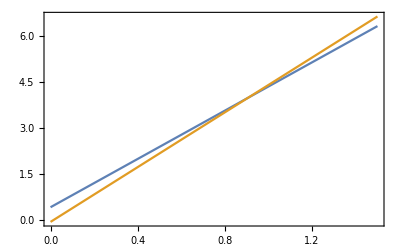

InterpolatingFunction::dmval: Input value {1.00031} lies outside the range of data in the interpolating function. Extrapolation will be used.

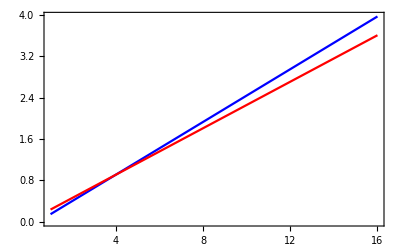

```mathematica
Plot[{xLatErVsSetpointVInterpolated[vv],yLatErVsSetpointVInterpolated[vv]}, {vv,0,1.5}]
Plot[{xLatSetpointVVsErInterpolated[Err],yLatSetpointVVsErInterpolated[Err]}, {Err,1,16}, PlotStyle -> {Blue, Red}]
```

```mathematica
tab = Table[{Err, xLatSetpointVVsErInterpolated[Err],yLatSetpointVVsErInterpolated[Err]}, {Err,3,8,0.5}] // MatrixForm;
Print["Lat depth [Er], X setpoint [V], Y setpoint [V]"]
Print[tab]
```

InterpolatingFunction::dmval: Input value {3.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Lat depth [Er], X setpoint [V], Y setpoint [V]

(3. | 0.658029 | 0.687259
3.5 | 0.785335 | 0.799496
4. | 0.912642 | 0.911734
4.5 | 1.03995 | 1.02397
5. | 1.16726 | 1.13621
5.5 | 1.29456 | 1.24845
6. | 1.42187 | 1.36068
6.5 | 1.54918 | 1.47292
7. | 1.67648 | 1.58516
7.5 | 1.80379 | 1.69739
8. | 1.93109 | 1.80963)

#### Explore U/t values

Historical table at 152 Gauss
	-Graphics-

We can take these and use the ratio of scattering length at desired field vs 152 G to get approximate U/t.

```mathematica
ascatNormed[B_]:= 1 - 7/(B-202.1)
UratioVs152G[B_]:=ascatNormed[B]/ascatNormed[152.1]
```

Approximate U/t at a few lattice depths at 203.5 G

```mathematica
{{4,UratioVs152G[203.5]*1.022},
{4.5,UratioVs152G[203.5]*1.309},
{5.0,UratioVs152G[203.5]*1.654},
{5.5,UratioVs152G[203.5]*2.06},
{6.0,UratioVs152G[203.5]*2.547},
{6.5,UratioVs152G[203.5]*3.123}} // MatrixForm
```

(4 | -3.58596
4.5 | -4.59298
5. | -5.80351
5.5 | -7.22807
6. | -8.93684
6.5 | -10.9579)